#### Problem 9.2.13b

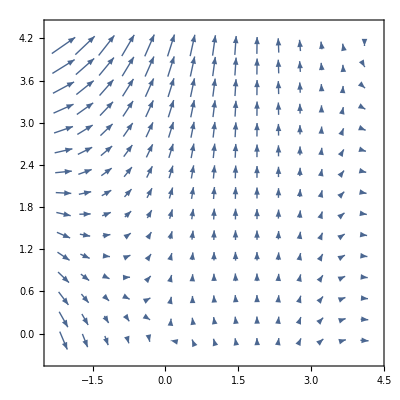

```mathematica
VectorPlot[{(2-x)*(y-x),(4-x)*(y+x)}, {x,-2.1,4.1},{y, -0.1,4.1}]
```

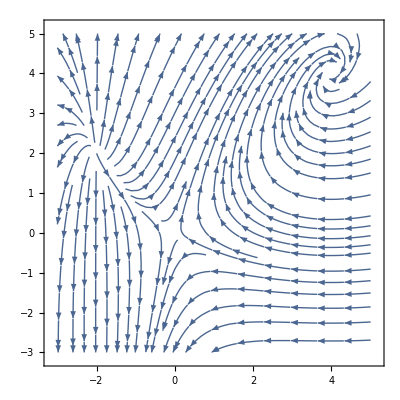

```mathematica
StreamPlot[{(2+x)*(y-x),(4-x)*(y+x)}, {x,-3,5},{y, -3,5}]
```

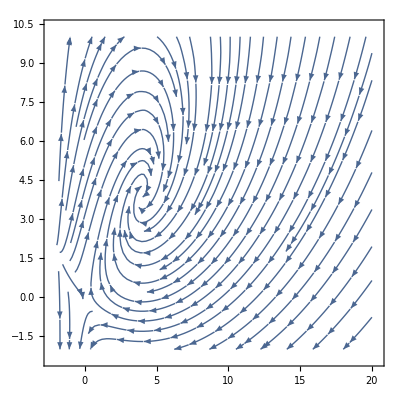

```mathematica
StreamPlot[{(2+x)*(y-x),(4-x)*(y+x)}, {x,-2,20},{y, -2,10}]
```

#### Problem 9.2.22b

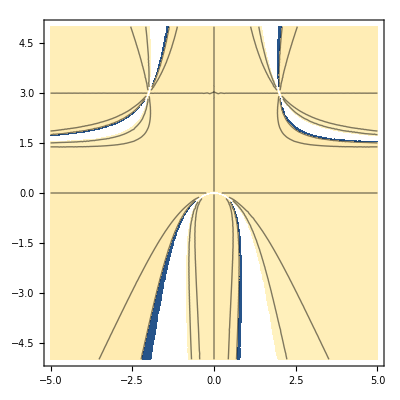

```mathematica
ContourPlot[(-2*x*(y^2)+6*x*y)/(2*(x^2)*y-3*(x^2)-4*y), {x,-5,5}, {y,-5,5}]
```

#### Problem 9.3.9

Part A

```mathematica
Solve[{(2+y)*(y-0.5)==0,(2-x)*(y+0.5*x)==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.,y→0.5},{x→4.,y→-2.},{x→2.,y→-2.},{x→2.,y→0.5}}

```mathematica
(2+y)*(y-0.5)
```

(-0.5+y) (2+y)

```mathematica
Expand[(-0.5+y) (2+y)]
```

-1.+1.5 y+y^2

```mathematica
(2-x)*(y+0.5*x)
```

(2-x) (0.5 x+y)

```mathematica
Expand[(2-x) (0.5 x+y)]
```

1. x-0.5 x^2+2 y-x y

```mathematica
J9[x_,y_]:={{0,1.5+2*y},{1-x-y,2-x}}
```

Part B

```mathematica
List[J9[-1,0.5],J9[4,-2],J9[2,-2],J9[2,0.5]]
```

{{{0,2.5},{1.5,3}},{{0,-2.5},{-1,-2}},{{0,-2.5},{1,0}},{{0,2.5},{-1.5,0}}}

Part C

```mathematica
List[{Det[{{0,2.5},{1.5,3}}-{{a,0},{0,a}}],Det[{{0,-2.5},{-1,-2}}-{{a,0},{0,a}}],Det[{{0,-2.5},{1,0}}-{{a,0},{0,a}}],Det[{{0,2.5},{-1.5,0}}-{{a,0},{0,a}}]}]
```

{{-3.75-3 a+a^2,-2.5+2 a+a^2,2.5+a^2,3.75+a^2}}

```mathematica
List[Solve[-3.75-3 a+a^2==0,a],Solve[-2.5+2 a+a^2==0,a],Solve[2.5+a^2==0,a],Solve[3.75+a^2==0,a]]
```

{{{a→-0.94949},{a→3.94949}},{{a→-2.87083},{a→0.870829}},{{a→0.-1.58114 ⅈ},{a→0.+1.58114 ⅈ}},{{a→0.-1.93649 ⅈ},{a→0.+1.93649 ⅈ}}}

Part D

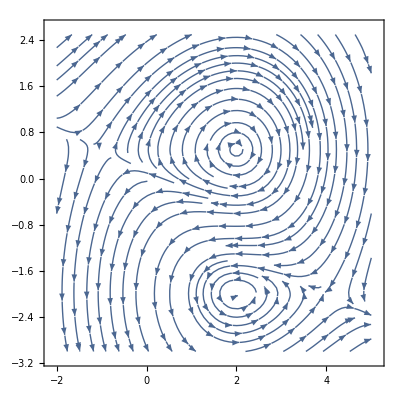

```mathematica
StreamPlot[{(2+y)*(y-0.5),(2-x)*(y+0.5*x)},{x,-2,5},{y,-3,2.5}]
```

#### Problem 9.3.11bcd

Part A

```mathematica
Solve[{2*x+y+x*(y^3)==0, x-2*y-x*y==0},{x,y}]
```

{{x→0,y→0},{x→1/54 (-33+√2019-6/(45-√2019)+(6 6^(1/3))/(45-√2019)^(2/3)-(6 6^(2/3))/(45-√2019)^(1/3)-6 (6 (45-√2019))^(1/3)+(6 (45-√2019))^(2/3)),y→-(45-√2019)^(1/3)/6^(2/3)-1/(6 (45-√2019))^(1/3)},{x→1/108 (-66+2 √2019-12/(45-√2019)-(6 ⅈ 2^(1/3) 3^(5/6))/(45-√2019)^(2/3)-(6 6^(1/3))/(45-√2019)^(2/3)-(18 ⅈ 2^(2/3) 3^(1/6))/(45-√2019)^(1/3)+(6 6^(2/3))/(45-√2019)^(1/3)+6 ⅈ 3^(5/6) (2 (45-√2019))^(1/3)+3 ⅈ 3^(1/6) (2 (45-√2019))^(2/3)+6 (6 (45-√2019))^(1/3)-(6 (45-√2019))^(2/3)),y→((1+ⅈ √3) (45-√2019)^(1/3))/(2 6^(2/3))+(1-ⅈ √3)/(2 (6 (45-√2019))^(1/3))},{x→1/108 (-66+2 √2019-12/(45-√2019)+(6 ⅈ 2^(1/3) 3^(5/6))/(45-√2019)^(2/3)-(6 6^(1/3))/(45-√2019)^(2/3)+(18 ⅈ 2^(2/3) 3^(1/6))/(45-√2019)^(1/3)+(6 6^(2/3))/(45-√2019)^(1/3)-6 ⅈ 3^(5/6) (2 (45-√2019))^(1/3)-3 ⅈ 3^(1/6) (2 (45-√2019))^(2/3)+6 (6 (45-√2019))^(1/3)-(6 (45-√2019))^(2/3)),y→((1-ⅈ √3) (45-√2019)^(1/3))/(2 6^(2/3))+(1+ⅈ √3)/(2 (6 (45-√2019))^(1/3))}}

```mathematica
N[%27]
```

{{x→0.,y→0.},{x→-1.19345,y→-1.4797},{x→-1.56994-1.76673 ⅈ,y→0.739852-1.06871 ⅈ},{x→-1.56994+1.76673 ⅈ,y→0.739852+1.06871 ⅈ}}

Part B

```mathematica
List[J11[0,0],J11[-1.1934523728733766,-1.4797047722094023],J11[-1.5699404802299195-1.7667263056477176 ⅈ,0.7398523861047012-1.0687116822017335 ⅈ],J11[-1.5699404802299195+1.7667263056477176 ⅈ,0.7398523861047012+1.0687116822017335 ⅈ]]
```

{{{2,1},{1,-2}},{{-1.23985,-6.83929},{2.4797,-0.806548}},{{-0.130074-0.534356 ⅈ,-4.58036+10.6004 ⅈ},{0.260148+1.06871 ⅈ,-0.43006+1.76673 ⅈ}},{{-0.130074+0.534356 ⅈ,-4.58036-10.6004 ⅈ},{0.260148-1.06871 ⅈ,-0.43006-1.76673 ⅈ}}}

Part C

```mathematica
List[{Det[{{2,1},{1,-2}}-{{a,0},{0,a}}],Det[{{-1.2398523861046438,-6.839285762759309},{2.479704772209402,-0.8065476271266234}}-{{a,0},{0,a}}],Det[{{-0.13007380694759085-0.5343558411008673 ⅈ,-4.580357118620114+10.600357833885994 ⅈ},{0.26014761389529883+1.0687116822017335 ⅈ,-0.4300595197700805+1.7667263056477176 ⅈ}}-{{a,0},{0,a}}],Det[{{-0.13007380694759085+0.5343558411008673 ⅈ,-4.580357118620114-10.600357833885994 ⅈ},{0.26014761389529883-1.0687116822017335 ⅈ,-0.4300595197700805-1.7667263056477176 ⅈ}}-{{a,0},{0,a}}]}]
```

{{-5+a^2,17.9594+2.0464 a+a^2,(13.5203+2.13742 ⅈ)+(0.560133-1.23237 ⅈ) a+a^2,(13.5203-2.13742 ⅈ)+(0.560133+1.23237 ⅈ) a+a^2}}

```mathematica
List[Solve[-5+a^2==0,a],Solve[17.95940954441806+2.046400013231267 a+a^2==0,a],Solve[(13.520295227789953+2.1374233644035323 ⅈ)+(0.5601333267176714-1.2323704645468503 ⅈ) a+a^2==0,a],Solve[(13.520295227789953-2.1374233644035323 ⅈ)+(0.5601333267176714+1.2323704645468503 ⅈ) a+a^2==0,a]]
```

{{{a→-√5},{a→√5}},{{a→-1.0232-4.11248 ⅈ},{a→-1.0232+4.11248 ⅈ}},{{a→-0.612621+4.34876 ⅈ},{a→0.0524876-3.11639 ⅈ}},{{a→-0.612621-4.34876 ⅈ},{a→0.0524876+3.11639 ⅈ}}}

Part D

```mathematica
J11[x_,y_]:={{2+(y^3),1+3*x*(y^2)},{1-y,-2-x}}
```

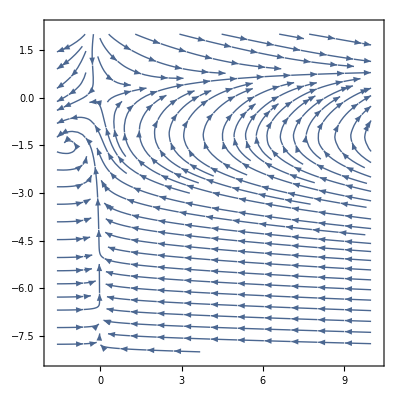

```mathematica
StreamPlot[{2*x+y+x*(y^3), x-2*y-x*y},{x,-1.6,10},{y,-8,2}]
```

#### Problem 9.3.14bcd

Part A

```mathematica
Solve[{1-x*y==0,x-y^3==0},{x,y}]
```

{{x→-1,y→-1},{x→ⅈ,y→-ⅈ},{x→-ⅈ,y→ⅈ},{x→1,y→1}}

Part B

```mathematica
List[J14[-1,-1],J14[ⅈ,-ⅈ],J14[-ⅈ,ⅈ],J14[1,1]]
```

{{{1,1},{1,-3}},{{ⅈ,-ⅈ},{1,3}},{{-ⅈ,ⅈ},{1,3}},{{-1,-1},{1,-3}}}

Part C

```mathematica
List[{Det[{{1,1},{1,-3}}-{{a,0},{0,a}}],Det[{{ⅈ,-ⅈ},{1,3}}-{{a,0},{0,a}}],Det[{{-ⅈ,ⅈ},{1,3}}-{{a,0},{0,a}}],Det[{{-1,-1},{1,-3}}-{{a,0},{0,a}}]}]
```

{{-4+2 a+a^2,4 ⅈ-(3+ⅈ) a+a^2,-4 ⅈ-(3-ⅈ) a+a^2,4+4 a+a^2}}

```mathematica
List[Solve[-4+2 a+a^2==0,a],Solve[4 ⅈ-(3+ⅈ) a+a^2==0,a],Solve[-4 ⅈ-(3-ⅈ) a+a^2==0,a],Solve[4+4 a+a^2==0,a]]
```

{{{a→-1-√5},{a→-1+√5}},{{a→1/2 ((3+ⅈ)-√(8-10 ⅈ))},{a→1/2 ((3+ⅈ)+√(8-10 ⅈ))}},{{a→1/2 ((3-ⅈ)-√(8+10 ⅈ))},{a→1/2 ((3-ⅈ)+√(8+10 ⅈ))}},{{a→-2},{a→-2}}}

Part D

```mathematica
J14[x_,y_]:={{-y,-x},{1,-3*(y^2)}}
```

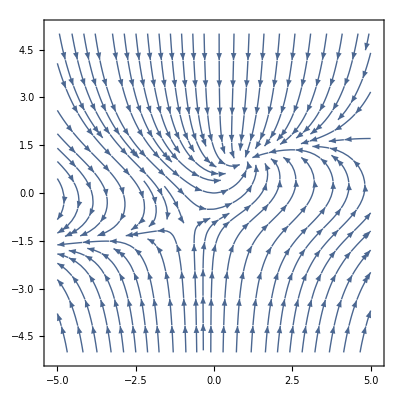

```mathematica
StreamPlot[{1-x*y,x-y^3},{x,-5,5},{y,-5,5}]
```

```mathematica
NDSolve[
```